# Newtons Method

There is no formula to solve f(x)=0 unless f is linear, a low degree polynomials in a scalar variable x, or a very simple trig function!  The only option in general is an iterative numerical approximation.  You learned how to implement a 1D Newtons Method in Calculus!  We are going to do a quick review

## Newton 1D f(x)=0 with f:ℝ→ℝ

Suppose we want so solve f(x)=0 and we have a reasonable first guess x_0.  We want to improve this guess to a hopefully better approximation x_1 in a systematic way.  The local linear approximation near x_0 is 
	f(x)≈f(x_0)+f'(x_0)(x-x_0)
Newton’s method consists of setting the approximation to zero
	 f(x_0)+f'(x_0)(x-x_0)=0
and calling the hopefully improved solution x_1.  In other words, 
	x_1=x_0-f(x_0)/f'(x_0).

The plan is to do this iteratively until the iterates x_k get stuck or converges.   This is easy to implement and in practice it converges very fast if the initial guess is good.

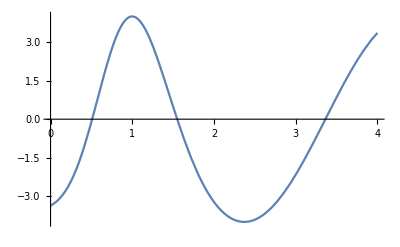

```mathematica
f[x_]:= 4Sin[x ArcTan[x +E^(x^2)]- Cos[x+Sin[x]]]
Plot[f[x],{x, 0, 4},PlotRange->All]
x0=1.4;
Newton[f_][x_]:= x-f[x]/f'[x]
NestList[ Newton[f],x0,4]
```

```mathematica
{1.4,1.5499526856896229,1.54986539539521,1.5498653979942159,1.5498653979942156}
```

```mathematica
f[1.5498653979942156]
```

4.89859×10^-16

## Newton 1D g(x)=x with g:ℝ→ℝ

Suppose we want so solve g(x)=x and we have a reasonable first guess x_0.  We want to improve this guess to a hopefully better approximation x_1 in a systematic way.  The local linear approximation near x_0 is 
	g(x)≈g(x_0)+g'(x_0)(x-x_0)
Newton’s method consists of setting the approximation equal to x
	 g(x_0)+g'(x_0)(x-x_0)=x
and calling the hopefully improved solution x_1.  In other words, 
	x_1=(g(x_0)-g'(x_0)x_0)/(1-g'(x_0))

The plan is to do this iteratively until the iterates x_k get stuck or converge.   This is easy to implement and in practice it converges very fast if the initial guess is good.

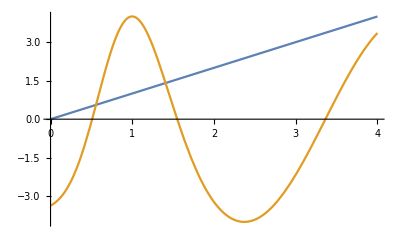

```mathematica
g[x_]:= 4Sin[x ArcTan[x +E^(x^2)]- Cos[x+Sin[x]]]
Plot[{x,g[x]},{x, 0, 4},PlotRange->All]
x0=0.5;
NewtonFP[g_][x_]:= (g[x]-g'[x]x)/(1-g'[x])
NestList[ NewtonFP[g],x0,4]
```

```mathematica
{0.5,0.5577694189833028,0.5564526953627974,0.5564524470678939,0.5564524470678845}
```

## Newton 2D f(x)=0 with f:ℝ^2→ℝ^2

Suppose we want so solve f(x)=0 and we have a reasonable first guess x_0.  We want to improve this guess to a hopefully better approximation x_1 in a systematic way.  The local linear approximation near x_0 is 
	f(x)≈f(x_0)+Df(x_0).(x-x_0)
Newton’s method consists of setting the approximation to zero
	 f(x_0)+Df(x_0).(x-x_0)=0
and calling the hopefully improved solution x_1.  In other words, 
	x_1=x_0-(Df(x_0))^-1.f(x_0).

The plan is to do this iteratively until the iterates x_k get stuck or converge.   This is easy to implement and in practice it converges very fast if the initial guess is good.

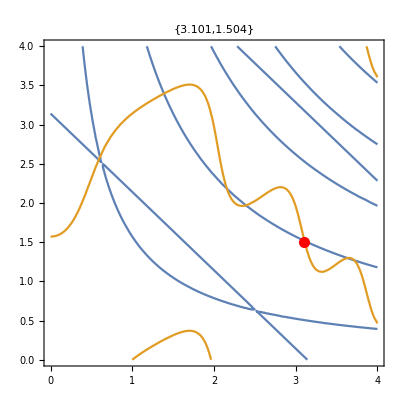

{{3.101,1.504},{3.10652,1.517},{3.10652,1.51694},{3.10652,1.51694},{3.10652,1.51694}}

```mathematica
f[{x1_,x2_}]:={Sin[x1+x2]*Cos[x1 x2],x1*Cos[x1+x2]-Cos[x2 - x1^2]}
x0={3.101,1.504};
ContourPlot[{f[{x1,x2}]⟦1⟧==0,f[{x1,x2}]⟦2⟧==0},{x1, 0, 4},{x2,0,4},
Epilog->{Red, PointSize[0.02],Point[x0]},PlotLabel->x0]
Df[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}];
Newton2D[f_,Df_][x_]:= x-LinearSolve[Df[x],f[x]];
NestList[ Newton2D[f,Df],x0,4]
```

## Newton 2D g(x)=x with g:ℝ^2→ℝ^2

The easiest thing to do is to convert this directly to the “f” form by defining 
	f(x)=g(x)-x
and using the “f” formula.  This gives
	x_1=x_0-(Dg(x_0)-Id)^-1.(g(x_0)-x_0)

The plan is to do this iteratively until the iterates x_k get stuck or converge.   This is easy to implement and in practice it converges very fast if the initial guess is good.

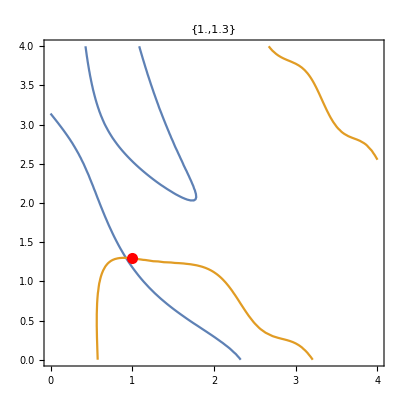

{{1.,1.3},{0.918198,1.30393},{0.922919,1.2997},{0.922912,1.29972},{0.922912,1.29972}}

```mathematica
g[{x1_,x2_}]:={3.2 Sin[x1+x2]*Cos[x1 x2],3x1*Sin[x1+x2]-Cos[x2 - x1^2]}
x0={1.0,1.3};
ContourPlot[{g[{x1,x2}]⟦1⟧-x1==0,g[{x1,x2}]⟦2⟧-x2==0},{x1, 0, 4},{x2,0,4},
Epilog->{Red, PointSize[0.02],Point[x0]},PlotLabel->x0]
Dg[{x1_,x2_}]=D[g[{x1,x2}],{{x1,x2}}];
Newton2DFP[g_,Dg_][x_]:= x-LinearSolve[Dg[x]-({{1, 0}, {0, 1}}),g[x]-x];
NestList[ Newton2DFP[g,Dg],x0,4]
```

## Newton 3D f(x)=0 with f:ℝ^3→ℝ^3

Suppose we want so solve f(x)=0 and we have a reasonable first guess x_0.  We want to improve this guess to a hopefully better approximation x_1 in a systematic way.  The local linear approximation near x_0 is 
	f(x)≈f(x_0)+Df(x_0).(x-x_0)
Newton’s method consists of setting the approximation to zero
	 f(x_0)+Df(x_0)(x-x_0)=0
and calling the hopefully improved solution x_1.  In other words, 
	x_1=x_0-(Df(x_0))^-1 f(x_0).

The plan is to do this iteratively until the iterates x_k get stuck or converge.   This is easy to implement and in practice it converges very fast if the initial guess is good.

```mathematica
f[{x1_,x2_,x3_}]:={Sin[x1+x2+Cos[x1 x3]],x1*Cos[x1+x2+x3]-Cos[x2 - x1^2],Cos[x1+x3-0.3x1 x2]}
x0={0.2,1.8,1.8};
Show[
ContourPlot3D[{f[{x1,x2,x3}]⟦1⟧==0,f[{x1,x2,x3}]⟦2⟧==0,f[{x1,x2,x3}]⟦3⟧==0},{x1, 0, 2},{x2,0,2},{x3,0,2}],
Graphics3D[{Red, PointSize[0.02],Point[x0]}],PlotLabel->x0,AxesLabel->{"x1","x2","x3"}]
Df[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}];
Newton2D[f_,Df_][x_]:= x-LinearSolve[Df[x],f[x]];
NestList[ Newton2D[f,Df],x0,14]
```

-Graphics3D-

{{0.2,1.8,1.8},{0.325417,1.93582,1.41773},{0.306744,1.93109,1.44173},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185},{0.30654,1.93115,1.44185}}

## Newton f(x)=0 and g(x)=x with f:ℝ^n→ℝ^n and g:ℝ^n→ℝ^n

The derivation does not really care about the dimension!  The update formula 
	x_(k+1)=x_k-(Df(x_k))^-1.f(x_k)
is identical.  Finding good initial guesses is MUCH harder when you can not plot things!  To get the Fixed Point version just put 
	f(x)=g(x)-x and of course Df(x)=Dg(x)-Id_n

## FindRoot and Periodic Orbits

Essentially FindRoot implements all this (with a few bells and whistles) for you without thinking about it for simple functions. We are going to build ourselves a Newton fixed point solver that uses the Jacobian sensitivity directly.